```mathematica
MapaProjekta=ParentDirectory[NotebookDirectory[],2]<>"\\";
MapaD=MapaProjekta<>"DATOTEKE\\";
MapaD1=MapaD<>"Normalne\\";
```

# UVAŽANJE, IZVAŽANJE

Glej poglavje DATOTEKE

```mathematica
SystemOpen/@{
NotebookDirectory[]<>"08) DATOTEKE.nb"
};
```

BISTVENO:

Audio

AudioData

Image

ImageData

Video

VideoExtractFrames[vid, Interval@{12,13}]

AnimationVideo[slika[it],itspec]

In pa tadolga ffmpeg vrjanta

# ZVOK

## SPLOŠNO

```mathematica
a=Audio[MapaD1<>"Ugani kdo je to.mp3"];
ad=AudioData@a;
```

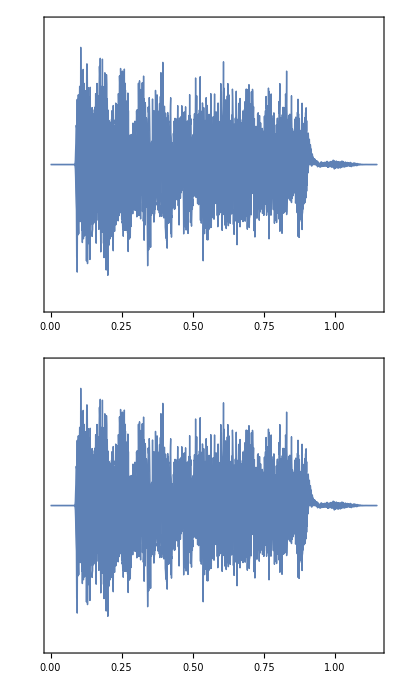

```mathematica
AudioPlot@a
```

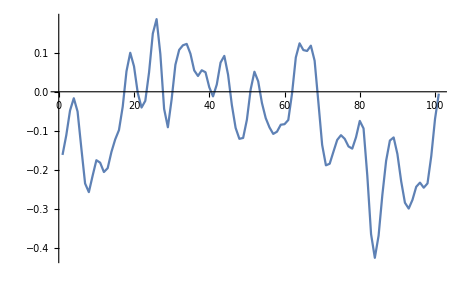

```mathematica
ListLinePlot@ad[[1,10000;;10100]]
```

```mathematica
sr=44100;

{šum,rastoče}=Audio[#,SampleRate->sr]&/@{
	RandomReal[{-1,1},100000],
	α=2π*1000.0; T=20.0; Sin[α/2.0 Range[0,T,1/sr]^2]
}
```

{,}

```mathematica
QuantityMagnitude@AudioSampleRate@šum
```

44100

## UČASIH PRIDE PRAV

Branje

```mathematica
k=Range[10,1,-1];
AudioPlay@Audio@SpeechSynthesize[ToString[k]<>", Liftoff!",Language->"English"];
```

```mathematica
k=200;
AudioPlay@Audio@SpeechSynthesize[
	ToString[k]<>" more steps to compute",
	Language->"English"
];
```

Narek: morda bo nekega dne uporabno

```mathematica
SpeechRecognize[Audio@AudioCapture[Appearance->"Detailed"],TargetDevice->"GPU"]
```

mine craft god of war ancient dalians verbal space program well from mathematic

# SLIKE

## SPLOŠNO

Z enako velikimi lahko kar direktno računamo

```mathematica
(-Graphics-+-Graphics-)/2.123
```

-Graphics-

Spremenimo velikost:

```mathematica
s=-Graphics-;
sre1=ImageResize[s,100]
sre2=ImageResize[s,{100,30}]
```

-Graphics-

-Graphics-

```mathematica
ImageDimensions/@{s,sre1,sre2}
```

{{1920,1080},{100,56},{100,30}}

Lahko Array flatten ali pa tole direktno na slikah:

```mathematica
sestavljena=ImageAssemble@({{-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}})
```

-Graphics-

Lahko kolaž nrdimo

```mathematica
OdLeveProtiDesni=.75;
OdDolProtiGor=.27;
ImageCompose[-Graphics-,ImageResize[-Graphics-,50],Scaled[{OdLeveProtiDesni,OdDolProtiGor}]]
```

-Graphics-

probej še s seznami (poglavje arraysi  [[]] ). Pozor slika je v arrayu zapisana “od zgoraj navzdol”(kot bi brali vrstice)

```mathematica
SystemOpen[NotebookDirectory[]<>"05) SEZNAMI.nb"]
```

## ZELO OSNOVNO ODSTRANJEVANJE ENOTNEGA OZADJA IN PODOBNO

```mathematica
RemoveBackground[-Graphics-]
```

-Graphics-

```mathematica
sp=ImageData[%];
α=sp[[;;,;;,4]];
Image@α
```

-Graphics-

ali pa, če sami to nardimo, pa naj bo vsaj mal zašumljena

```mathematica
s0=-Graphics-;
šum=.1 RandomReal[{-1,1},Dimensions@ImageData@s0];
šum[[;;,;;,4]]=0;
s=s0+Image@šum
```

-Graphics-

kakšno barvo pričakujemo za ozadje

```mathematica
sp=ImageData@s;
ozadje=Mean@Mean@sp[[;;,;;50]]
```

{0.00796431,0.772007,0.28981,1.}

```mathematica
razlike=Map[
	Norm,
	sp-ConstantArray[ozadje,Dimensions[sp][[;;2]]],
	{2}
];

Image@razlike
```

-Graphics-

```mathematica
ϵ=.3;

Image@((1+Sign[razlike-ϵ])/2)
```

-Graphics-

Pozor: v praksi (pri fizikalnih eksperimentih) se stvari pogosto dosti bolj zakomplicirajo in je treba veliko probavanja in ustvarjalnosti.

Učasih se tut splača sprobat kakga druzga od ugrajenih filtrov in podobnih stvari, k jih je res velik.

https://reference.wolfram.com/language/guide/MathematicalMorphology.html?v=13.1

https://reference.wolfram.com/language/guide/SegmentationAnalysis.html

Tale pogosto prou pride. Lahko za izziv sami probate napisat, ampak je vgrajen sigurno parkrat hitrejši

```mathematica
Colorize@MorphologicalComponents@-Graphics-
```

-Graphics-

Pa tut razne ai stvari

https://reference.wolfram.com/language/guide/ComputerVision.html?v=13.1

```mathematica
ImageRestyle[-Graphics-, 0.3 -> -Graphics-,TargetDevice->"GPU"]
```

-Graphics-

# VIDEO

## KRAJŠI POSNETKI

Ni kej dost za povedat. Glej poglavje datoteke: kako se jih importa, exporta

Sicer se pa pač posebi dela s slikami pa z zvokom

Glejte video o sledenju gibanju s posnetka

## DALJŠI POSNETKI (OD NEKAJ 10 SEKUND)

Nikar direkt v slike!!!, ker vam zabije RAM in krešne računalnik.

Pač pa: VideoMapList[f[#Image]&,video]

## ŠE DALJŠI, ZELO VELIKI POSNETKI

Zelo velikih videov NE uvažamo v Mathematico.

V video editorju jih izvozmo kot slike v neko mapo in potem v Mathematico uvažamo sliko po sliko

Lahko pa tudi v video editorju razdelimo na krajše videe

# GLEJ TUDI

https://www.youtube.com/watch?v=gnUYoQ1pwes&ab_channel=KuvinaSaydaki